```mathematica
gerPoly = GeoPosition[CountryData["Germany", "Coordinates"]];
```

```mathematica
gridPoly = GeoGridPosition[gerPoly, {"AzimuthalEquidistant",  "Centering"-> GeoPosition[{51.16, 10.45}]}][[1]];
```

```mathematica
gerOutline = Graphics[{Black, Line[ gridPoly]}];
```

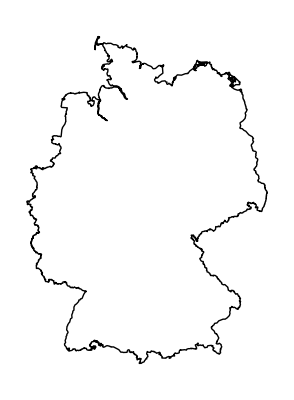

```mathematica
gerOutline
```

WolframAlphaQueryResults

348 672 km^2  (square kilometers)  (world rank: 63^rd)

```mathematica
CountryData[{"Saarland", "Germany"}, "Coordinates"]
```

CountryData::notent: {"Saarland", "Germany"} is not a known entity, class, or tag for CountryData. Use CountryData[] for a list of entities.

CountryData[{Saarland,Germany},Coordinates]

```mathematica
sl = Entity["AdministrativeDivision",{"Saarland","Germany"}]
```

Saarland, Germany

```mathematica
Entity["Country", "Germany"]["Coordinates"]
```

Missing[UnknownProperty,{Country,Coordinates}]

```mathematica
CountryData[Entity["AdministrativeDivision",{"Saarland","Germany"}], "Coordinates"]
```

CountryData::notent: Entity["AdministrativeDivision", {"Saarland", "Germany"}] is not a known entity, class, or tag for CountryData. Use CountryData[] for a list of entities.

CountryData[Saarland, Germany,Coordinates]

```mathematica
slPol = EntityValue[sl, "Polygon"]
```

Polygon[GeoPosition[…]]

```mathematica
slPoly = GeoGridPosition[slPol[[1]], {"AzimuthalEquidistant",  "Centering"-> GeoPosition[{51.16, 10.45}]}][[1, 1]];
```

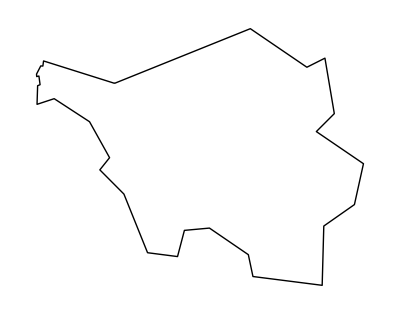

```mathematica
slOutline = Graphics[{Black, Line[Join[slPoly, {slPoly[[1]]}]]}]
```

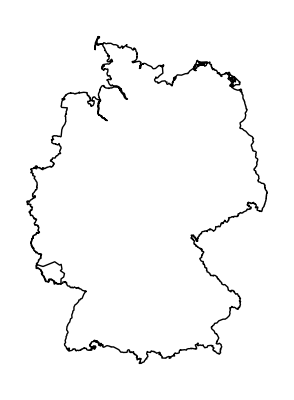

```mathematica
Show[{slOutline, gerOutline}]
```

```mathematica
EntityList[{"AdministrativeDivision", "Germany"}]
```

EntityList::noent: {AdministrativeDivision,Germany} is not an entity.

EntityList[{AdministrativeDivision,Germany}]

```mathematica
EntityClass["AdministrativeDivision", {"Country" -> "Germany"}]
```

```mathematica
blList = EntityList[EntityClass["AdministrativeDivision", {"Country" -> "Germany"}]][[1;;16]];
blList = Drop[Drop[blList, {4, 8, 4}], {9}];
blPolList = EntityValue[#, "Polygon"][[1]]& /@ blList;
coordList = GeoGridPosition[#, {"AzimuthalEquidistant",  "Centering"-> GeoPosition[{51.16, 10.45}]}][[1, 1]] & /@ blPolList;
outList = Graphics[ { Black, Line[Join[#, {#[[1]]}]] } ]& /@ coordList;
```

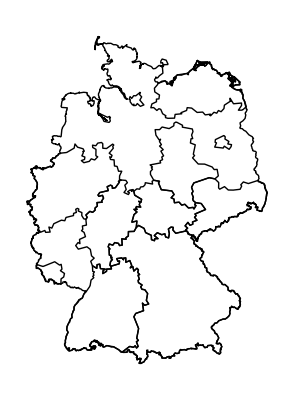

```mathematica
Show[{outList, gerOutline}]
```

```mathematica
ImageMeasurements[Out[113], "Entropy"]
```

0.66689